initValuesList = {1,2,3,4,5,6,7,8,9,10}

initValuesDerivativeList = {0,0,0,0,0,0,0,0,0,0}

Direct call to NDSolve.

sol

---------------------------------------------

stepCount = 0, t = 0.000895859, time used = 0.002002

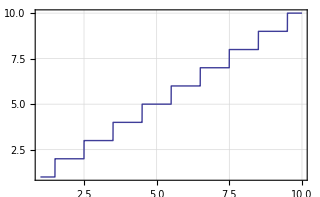

Plot

tPlot = 0.1

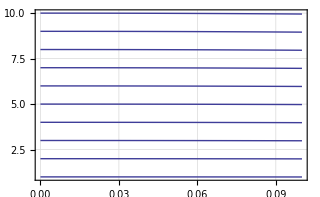

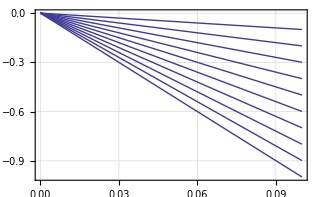

Hamiltonian

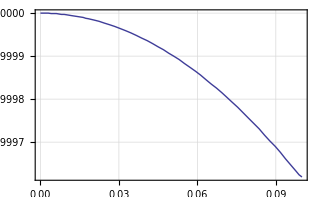

Kinetic and Potential Energy

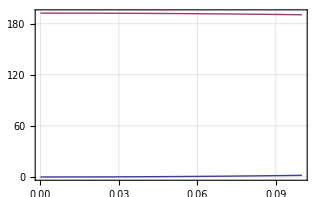

Using Apply to call NDSolve.

---------------------------------------------

stepCount = 0, t = 0.01, time used = 0.002001

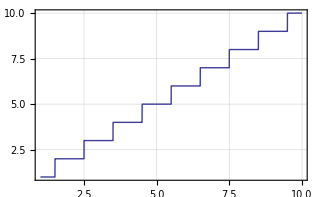

Plot

tPlot = 0.1

-Graphics-

-Graphics-

Hamiltonian

-Graphics-

Kinetic and Potential Energy

-Graphics-

---------------------------------------------

coords = {0.,0.000895859,0.00179172,0.00268758,0.00358344,0.0044793,0.00537516,0.00627101,0.00716687,0.00806273,0.00895859,0.00985445,0.0107503,0.0116462,0.012542,0.0134379,0.0143337,0.0152296,0.0161255,0.0170213,0.0179172,0.018813,0.0197089,0.0206048,0.0215006,0.0223965,0.0232923,0.0241882,0.0250841,0.0259799,0.0268758,0.0277716,0.0286675,0.0295634,0.0304592,0.0313551,0.0322509,0.0331468,0.0340427,0.0349385,0.0358344,0.0367302,0.0376261,0.0385219,0.0394178,0.0403137,0.0412095,0.0421054,0.0430012,0.0438971,0.044793,0.0456888,0.0465847,0.0474805,0.0483764,0.0492723,0.0501681,0.051064,0.0519598,0.0528557,0.0537516,0.0546474,0.0555433,0.0564391,0.057335,0.0582309,0.0591267,0.0600226,0.0609184,0.0618143,0.0627101,0.063606,0.0645019,0.0653977,0.0662936,0.0671894,0.0680853,0.0689812,0.069877,0.0707729,0.0716687,0.0725646,0.0734605,0.0743563,0.0752522,0.076148,0.0770439,0.0779398,0.0788356,0.0797315,0.0806273,0.0815232,0.0824191,0.0833149,0.0842108,0.0851066,0.0860025,0.0868983,0.0877942,0.0886901,0.0895859,0.0904818,0.0913776,0.0922735,0.0931694,0.0940652,0.0949611,0.0958569,0.0967528,0.0976487,0.0985445,0.0992723,0.1}

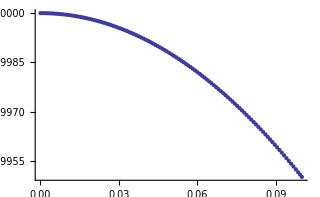

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
strSeparatorSmall="---------------------------------------------";

(* Numer of elements in the list *)
NoOfElements = 10;

DoPrint=False;
counter=0;
MaxNoOfSteps=10^6;
startingStepSizeVal =0.01;
maxStepSizeVal=0.01;
tMax=0.1;
stepN=1000;
tPlotMultiplier=1;

UU[xLst:{__}]:=Module[{retVal},
retVal=xLst . xLst /2;
Return[retVal];
];

(* Function, which accepts list of variables (xLst) and returns list of same length (retValLst) *)
listFunction[xLst:{__}]:=Module[{retValLst,listLen},
counter++;
If[DoPrint,Print["listFunction is called: ", counter," time(s) with xLst = ", ToString[xLst]]];
listLen=Length[xLst];
retValLst=Table[xLst[[ii]],{ii,1,listLen}];
Return[retValLst];
];

(* Function to plot vectors. *)
IndexedVariableFunc[idxVal_?NumericQ,vect_?VectorQ]:=Module[{idx,retVal,len},
len=Length[vect];
idx=Round[idxVal];
retVal=If[idx<1||idx>len,Indeterminate,vect[[idx]]];
Return[retVal];
];

(* Sorts second list using the normal ordering of the first one. *)
SortByFirst[lstOrder:{__},lstToBeSorted:{__}]:=Module[{retVal,nn,lst,lstSorted},
nn=Length[lstOrder];

If[Length[lstToBeSorted]≠ nn,(Print["SortByFirt::Lists have different length!"]; Return[Indeterminate];)];

lst=Table[{lstOrder[[ii]],lstToBeSorted[[ii]]},{ii,1,nn}];

lstSorted=SortBy[lst,First];
retVal=Table[lstSorted[[ii,2]],{ii,1,nn}];

Return[retVal];
];

(* Initial Values *)
initValuesList=Table[ii,{ii,1,NoOfElements}];
Print["initValuesList = ", initValuesList];

initValuesDerivativeList=Table[0,{ii,1,NoOfElements}];
Print["initValuesDerivativeList = ", initValuesDerivativeList];

IMAGESIZE=320;
defaultPltOpts:={PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Thick,ImageSize ->IMAGESIZE };

Print["Direct call to NDSolve."];
Print["sol"];

tStartNDSolve=AbsoluteTime[];
Clear[t,xxx,ppp,f,fp,TT,VV,HH];
stepCount=0;

sol=NDSolve[{D[xxx[t],{t,1}]== ppp[t],D[ppp[t],{t,1}]== -listFunction[xxx[t]],xxx[0]== initValuesList,ppp[0]== initValuesDerivativeList},{xxx,ppp},{t,0,tMax},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{xxx}},MaxSteps -> MaxNoOfSteps,
StepMonitor :> 
(
If[Mod[stepCount,stepN]==0,
(
tEndNDSolve=AbsoluteTime[];
Print[strSeparatorSmall];
Print["stepCount = ",stepCount, ", t = ", t,", time used = ",(tEndNDSolve-tStartNDSolve)];
sortArr=Sort[xxx[t]];
sortArrD=SortByFirst[xxx[t],xxx'[t]];Print[Plot[{IndexedVariableFunc[idx,sortArr],IndexedVariableFunc[idx,sortArrD]},{idx,1,NoOfElements},Evaluate[defaultPltOpts]]]
)
];
stepCount++;
)
];

Print["Plot"];
f=xxx/. sol[[1]];
fp=ppp/. sol[[1]];

tPlot=tPlotMultiplier*f["Domain"][[1,2]];
Print["tPlot = ", tPlot];

Print[Plot[f[t],{t,0,tMax}, PlotRange -> All, Frame -> True, PlotStyle -> Thick, GridLines -> Automatic]];
Print[Plot[fp[t],{t,0,tMax}, PlotRange -> All, Frame -> True, PlotStyle -> Thick, GridLines -> Automatic]];

Print["Hamiltonian"];
TT[t_]:=((fp[t]) . (fp[t])/2);
VV[t_]:=UU[f[t]];
HH[t_]:=TT[t]+VV[t];

Print[Plot[HH[t],{t,0,tPlot},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];

Print["Kinetic and Potential Energy"];
Print[Plot[{TT[t],VV[t]},{t,0,tPlot},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];

(* ============================================== *)

Print["Using Apply to call NDSolve."];

tStartNDSolve=AbsoluteTime[];
Clear[t,xxx,ppp,f,fp,TT,VV,HH];
stepCount=0;

eqAllLst:={D[xxx[t],{t,1}]== ppp[t],D[ppp[t],{t,1}]== -listFunction[xxx[t]],xxx[0]== initValuesList,ppp[0]== initValuesDerivativeList};
varList:={xxx,ppp};
tLst={t,0,tMax};

solveOptions={Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{xxx}},MaxSteps -> MaxNoOfSteps,StartingStepSize -> startingStepSizeVal,MaxStepSize -> maxStepSizeVal};

monitor:=(
If[Mod[stepCount,stepN]==0,
(
tEndNDSolve=AbsoluteTime[];
Print[strSeparatorSmall];
Print["stepCount = ",stepCount, ", t = ", t,", time used = ",(tEndNDSolve-tStartNDSolve)];
sortArr=Sort[xxx[t]];
sortArrD=SortByFirst[xxx[t],xxx'[t]];Print[Plot[{IndexedVariableFunc[idx,sortArr],IndexedVariableFunc[idx,sortArrD]},{idx,1,NoOfElements},Evaluate[defaultPltOpts]]]
)
];
stepCount++;
)

ndSolveLst:=Flatten[{{eqAllLst,varList,tLst},solveOptions,{StepMonitor :> monitor}},1];
solA=Apply[NDSolve,ndSolveLst];

Print["Plot"];
f=xxx/. sol[[1]];
fp=ppp/. sol[[1]];
ifun=First[xxx /. sol];

tPlot=tPlotMultiplier*f["Domain"][[1,2]];
Print["tPlot = ", tPlot];

Print[Plot[f[t],{t,0,tMax}, PlotRange -> All, Frame -> True, PlotStyle -> Thick, GridLines -> Automatic]];
Print[Plot[fp[t],{t,0,tMax}, PlotRange -> All, Frame -> True, PlotStyle -> Thick, GridLines -> Automatic]];

Print["Hamiltonian"];
TT[t_]:=((fp[t]) . (fp[t])/2);
VV[t_]:=UU[f[t]];
HH[t_]:=TT[t]+VV[t];

Print[Plot[HH[t],{t,0,tPlot},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];

Print["Kinetic and Potential Energy"];
Print[Plot[{TT[t],VV[t]},{t,0,tPlot},Evaluate[defaultPltOpts]]];
PrintTimeUsed[];
(* ============================================== *)

coords=First[InterpolatingFunctionCoordinates[ifun]];

Print[strSeparatorSmall];
Print["coords = ", coords];

(*
Print[strSeparatorSmall];
Print["Transpose[ifun[coords]][[1]] = ", Transpose[ifun[coords]][[1]]];
*)

ListPlot[Transpose[{coords, Transpose[ifun[coords]][[1]]}]]
```